# hexatic phase

### data loading

```mathematica
p0s={3.85,3.825,3.80,3.75};
```

```mathematica
temperatures={{0.039 ,0.016, 0.01 ,0.005 ,0.00385, 0.0025 ,0.002, 0.001 ,0.0005 ,0.00033 ,0.00025, 0.00014, 0.000091,0.000077,0.000054, 0.000045, 0.000036},{0.063 ,0.039, 0.03105, 0.016 ,0.01, 0.008, 0.0063, 0.005 ,0.00385, 0.0031, 0.0025, 0.002, 0.0015, 0.001, 0.00067 ,0.0005},{0.063 ,0.039 ,0.03105, 0.025, 0.016 ,0.01 ,0.008 ,0.0063, 0.005, 0.00385, 0.0031, 0.0028 ,0.0025 ,0.0022},{0.063, 0.039, 0.03105, 0.025 ,0.02, 0.016, 0.014,0.012 ,0.011, 0.01, 0.0093}};
 records={{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19}};
```

```mathematica
orientationals=Table[Table[DeleteCases[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/N4096/orderParameter/p","/orientationReIm_N4096_p","_T","_",".nc"},{p0s[[p]],p0s[[p]],temperatures[[p,T]],records[[p,i]]},{3,3,8,0}],"Data"],{i,Length[records[[p]]]}],$Failed],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

```mathematica
translationals=Table[Table[DeleteCases[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/N4096/orderParameter/p","/translationReIm_N4096_p","_T","_",".nc"},{p0s[[p]],p0s[[p]],temperatures[[p,T]],records[[p,i]]},{3,3,8,0}],"Data"],{i,Length[records[[p]]]}],$Failed],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

```mathematica
Table[Table[Table[Length[orientationals[[p,T,i,1]]],{i,Length[orientationals[[p,T]]]}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

## order parameters

```mathematica
orientationalsReal=Table[Table[Flatten[Table[Table[orientationals[[p,T,i,1,rec]],{rec,Ceiling[4/5*Length[orientationals[[p,T,i,1]]]],Length[orientationals[[p,T,i,1]]]}],{i,Length[orientationals[[p,T]]]}]],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

```mathematica
orientationalsIm=Table[Table[Flatten[Table[Table[orientationals[[p,T,i,2,rec]],{rec,Ceiling[4/5*Length[orientationals[[p,T,i,1]]]],Length[orientationals[[p,T,i,1]]]}],{i,Length[orientationals[[p,T]]]}]],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

```mathematica
VarOri=Table[Table[Variance[Table[Sqrt[orientationalsIm[[p,T,rec]]^2+orientationalsReal[[p,T,rec]]^2],{rec,Length[orientationalsIm[[p,T]]]}]],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{0.000032152,0.0000423404,0.0000532172,0.0000674155,0.0000758918,0.0000890697,0.0000950338,0.000102647,0.000114988,0.000115247,0.000142081,0.000132976,0.000127265,0.000145642,0.000109447,0.000133393,0.000130127},{0.0000286883,0.0000365771,0.0000416835,0.0000661977,0.0000951568,0.000116785,0.0001866,0.000197927,0.000206486,0.000313572,0.000381199,0.000501117,0.00106108,0.00202961,0.00260923,0.000457498},{0.0000325093,0.0000409504,0.0000497999,0.0000708559,0.000130575,0.000241744,0.000495468,0.000913501,0.00220336,0.00374807,0.00135974,0.000561188,0.000305594,0.000160759},{0.0000444055,0.0000664275,0.000101391,0.000177653,0.000379926,0.0010854,0.00299127,0.00140131,0.000378916,0.000115527,0.0000567549}}

```mathematica
translationalReal=Table[Table[Flatten[Table[Table[translationals[[p,T,i,1,rec]],{rec,Ceiling[4/5*Length[translationals[[p,T,i,1]]]],Length[translationals[[p,T,i,1]]]}],{i,Length[translationals[[p,T]]]}]],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

```mathematica
translationalIm=Table[Table[Flatten[Table[Table[translationals[[p,T,i,2,rec]],{rec,Ceiling[4/5*Length[translationals[[p,T,i,1]]]],Length[translationals[[p,T,i,1]]]}],{i,Length[translationals[[p,T]]]}]],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

```mathematica
VarTrans=Table[Table[Variance[Table[Sqrt[translationalIm[[p,T,rec]]^2+translationalReal[[p,T,rec]]^2],{rec,Length[orientationalsIm[[p,T]]]}]],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{0.000074945,0.0000955438,0.000102095,0.000118162,0.000105318,0.000102319,0.000129002,0.00011896,0.000139303,0.000118502,0.000132987,0.000124468,0.000121356,0.000126371,0.00013151,0.000128368,0.000130721},{0.0000757485,0.000081951,0.0000894873,0.0000947169,0.000126979,0.000133571,0.000152742,0.000132361,0.000116762,0.000150614,0.000156888,0.000134644,0.000137525,0.000182093,0.000223099,0.000531316},{0.0000703611,0.0000926562,0.0000953505,0.0000964436,0.000107679,0.000163247,0.000129701,0.00016208,0.000215283,0.000191423,0.000507934,0.000403733,0.000516637,0.000565048},{0.0000802374,0.000105441,0.000122343,0.000130886,0.000168621,0.000173139,0.000215789,0.000675859,0.000087197,0.00043139,0.000288161}}

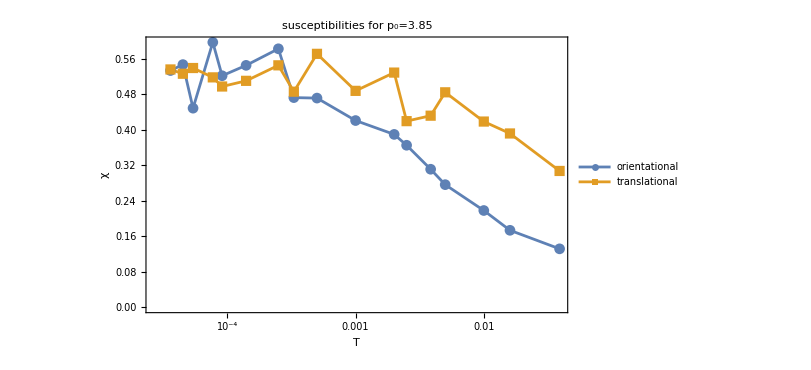
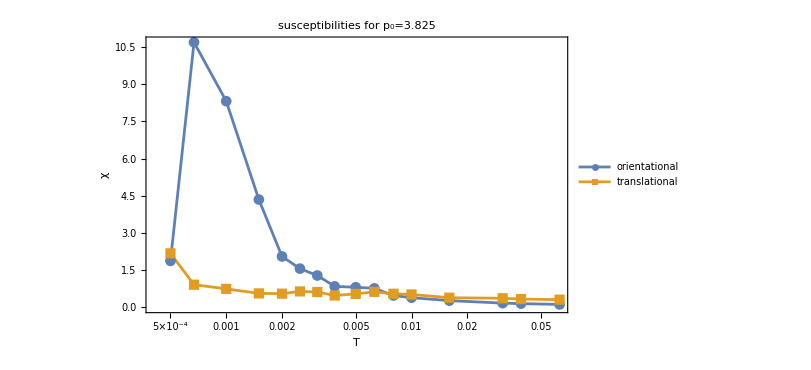
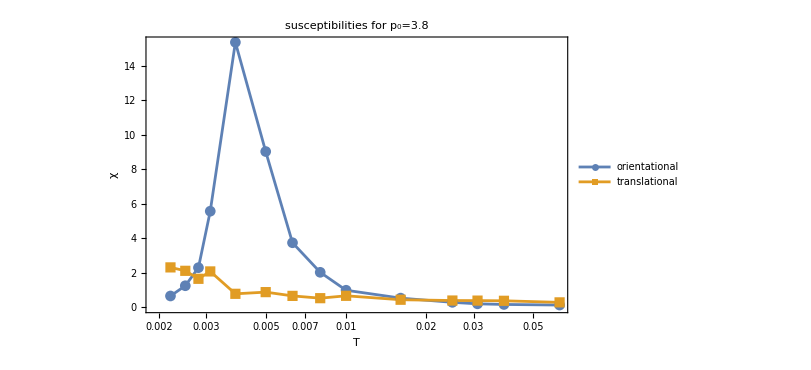
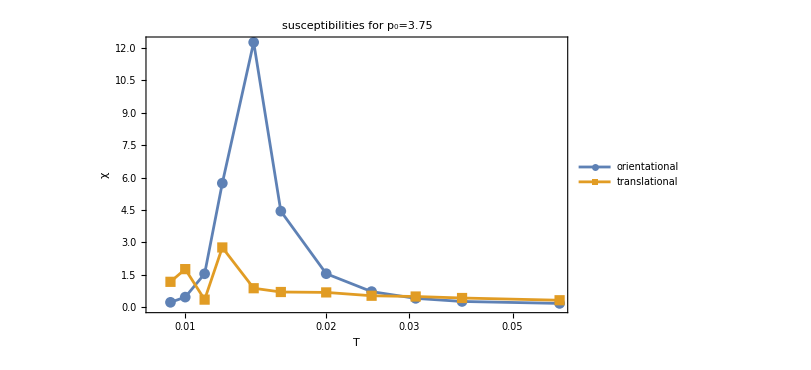

```mathematica
orderparameter=Table[ListLogLinearPlot[{Table[{temperatures[[p,T]],4096*VarOri[[p,T]]},{T,Length[temperatures[[p]]]}],Table[{temperatures[[p,T]],4096*VarTrans[[p,T]]},{T,Length[temperatures[[p]]]}]},PlotLegends->{"orientational","translational"},PlotStyle->Automatic,FrameLabel->{"T","χ"},ImageSize->600,PlotLabel->"susceptibilities for p_0="<>ToString[p0s[[p]]],Joined->True,PlotRange->All,PlotMarkers->Automatic],{p,Length[p0s]}]
```